## 平面内の直線のパラメーター表示とその描画

```mathematica
{3,0}+t{-5,2}
```

{3-5 t,2 t}

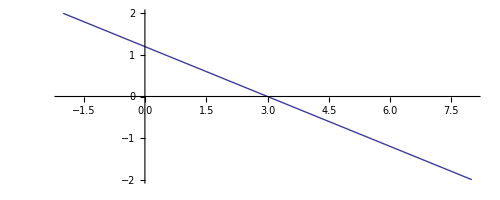

```mathematica
ParametricPlot[{3-5 t,2 t},{t,-1,1}]
```

## 平面内の直線の方程式とその描画

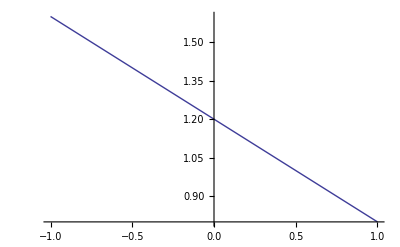

```mathematica
Plot[-2x/5+6/5,{x,-1,1}]
```

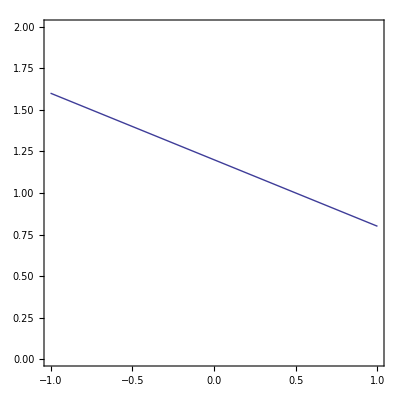

```mathematica
ContourPlot[2x+5y-6==0,{x,-1,1},{y,0,2}]
```

## 原点を中心とする回転

直線を回転させてみましょう．まず，回転行列（行列式が1の直交行列）を定義します．

```mathematica
R[s_]={{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}
```

{{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}

```mathematica
R[s]//MatrixForm
```

(Cos[s] | -Sin[s]
Sin[s] | Cos[s])

アニメーションの作成：

```mathematica
Animate[
Show[
ParametricPlot[{3-5 t,2 t},{t,-1,2},PlotRange->{{-4,4},{-4,4}}],
ParametricPlot[R[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Red]]
,{a,0,2Pi},SaveDefinitions->True]
```

「Manipulate」コマンドでもアニメーションがつくれます．「Animate」コマンドとどこが違うでしょうか？

```mathematica
Manipulate[
Show[
ParametricPlot[{3-5 t,2 t},{t,-1,2},PlotRange->{{-4,4},{-4,4}}],
ParametricPlot[R[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Red]]
,{a,0,2Pi},SaveDefinitions->True]
```

## 鏡映変換

鏡映変換もアニメーションにしてみましょう．鏡映は行列式が (-1) の直交行列を表現行列とする線形変換です．

```mathematica
r[s_]={{Cos[s],Sin[s]},{Sin[s],-Cos[s]}}
```

{{Cos[s],Sin[s]},{Sin[s],-Cos[s]}}

```mathematica
r[s]//MatrixForm
```

(Cos[s] | Sin[s]
Sin[s] | -Cos[s])

アニメーショにすると…

```mathematica
Animate[
Show[
ParametricPlot[{3-5 t,2 t},{t,-1,2},PlotRange->{{-4,4},{-4,4}}],
ParametricPlot[r[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Green]
]
,{a,0,2Pi},SaveDefinitions->True]
```

回転とあまり変わらないように感じますか？変換後の直線はどのような直線に関する鏡映でしょうか？それは下のアニメーションにおける赤い直線です．

```mathematica
Animate[
Show[
ParametricPlot[{3-5 t,2 t},{t,-1,2},PlotRange->{{-4,4},{-4,4}}],
ParametricPlot[r[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Green],
Plot[Tan[a/2]*x,{x,-4,4},PlotStyle->{Green,Dashed}]
]
,{a,0,2Pi},SaveDefinitions->True]
```

回転変換も同時に表してみました．鏡映変換は x軸に関する鏡映と回転変換の合成ですからね．

```mathematica
Animate[
Show[
ParametricPlot[{3-5 t,2 t},{t,-1,2},PlotRange->{{-4,4},{-4,4}}],
ParametricPlot[R[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Red],ParametricPlot[r[a].{3-5 t,2 t},{t,-1,2},PlotStyle->Green],
Plot[Tan[a/2]*x,{x,-4,4},PlotStyle->{Green,Dashed}]
]
,{a,0,2Pi},SaveDefinitions->True]
```